```mathematica
Get["http://iagomendes.com/GRVis.wl"]
```

Successfully loaded GRVis (version 1.0)

```mathematica
coords = {t, r, theta, phi}
M = 1;
metric = ({{-(1-M/(2 r))/(1 + M/(2 r)), 0, 0, 0}, {0, (1-M/(2 r))^4, 0, 0}, {0, 0, (1-M/(2 r))^4 r^2, 0}, {0, 0, 0, (1-M/(2 r))^4 r^2 Sin[theta]^2}})
metric // MatrixForm
```

(-(1-1/(2 r))/(1+1/(2 r)) | 0 | 0 | 0
0 | (1-1/(2 r))^4 | 0 | 0
0 | 0 | (1-1/(2 r))^4 r^2 | 0
0 | 0 | 0 | (1-1/(2 r))^4 r^2 Sin[theta]^2)

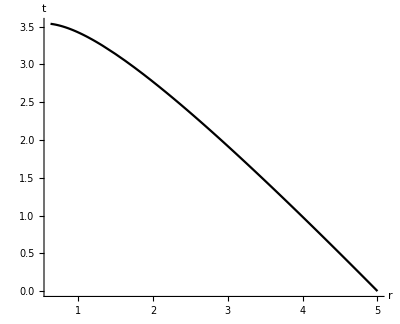

```mathematica
geodesics[{
{{0,5,Pi/2,0}, lorentzFactor[0.9999999]*{1,-0.9999999,0,0}, 0.001317}
}]
```